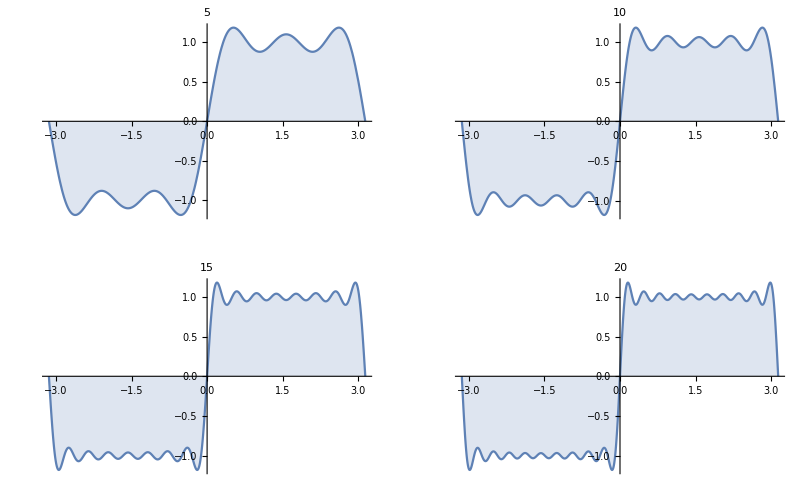

```mathematica
GraphicsGrid@Partition[ParallelTable[Plot[Evaluate[FourierTrigSeries[Sign[t],t,n]],{t,-π,π},Filling->Axis,PlotLabel->n],{n,5,25,5}],2]
```